# The Uncharted Method: Label Regularizations

## Abstract

Label Regularization is often not as preferred compared to other popular methods, such as Data Augmentation. 
Thus, there needs  more study on this subject. This notebook aims to explore novel approaches to Label Regularization, specifically Structural Label Smoothing (SLS) and Adaptive Label Regularization (ALR) proposed by the researchers. 
Finally, the evaluation will be based on a image classification task of CIFAR-100 dataset with a basic CNN.

## Data Preparation

### Load CIFAR-100

```mathematica
resource=ResourceObject["CIFAR-100"];
```

```mathematica
trainingData=ResourceData[resource,"TrainingData"];
testData=ResourceData[resource,"TestData"];

Length[trainingData]
Length[testData]
```

50000

10000

```mathematica
RandomSample[trainingData,5]
```

{-Graphics-→oak tree,-Graphics-→wardrobe,-Graphics-→snail,-Graphics-→crab,-Graphics-→rocket}

#### Since we are conducting a Single Task Object Classification, we use sublabels as the main label.

https://www.wolfram.com/language/11/neural-networks/object-classification.html.ko?product=language

```mathematica
classes=Union@Values[trainingData]
Length[classes]
```

{apple,aquarium fish,baby,bear,beaver,bed,bee,beetle,bicycle,bottle,bowl,boy,bridge,bus,butterfly,camel,can,castle,caterpillar,cattle,chair,chimpanzee,clock,cloud,cockroach,computer keyboard,couch,crab,crocodile,cup,dinosaur,dolphin,elephant,flatfish,forest,fox,girl,hamster,house,kangaroo,lamp,lawn-mower,leopard,lion,lizard,lobster,man,maple tree,motorcycle,mountain,mouse,mushroom,oak tree,orange,orchid,otter,palm tree,pear,pickup truck,pine tree,plain,plate,poppy,porcupine,possum,rabbit,raccoon,ray,road,rocket,rose,sea,seal,shark,shrew,skunk,skyscraper,snail,snake,spider,squirrel,streetcar,sunflower,sweet pepper,table,tank,telephone,television,tiger,tractor,train,trout,tulip,turtle,wardrobe,whale,willow tree,wolf,woman,worm}

100

## Constructing a CNN model

### Set up a CNN

#### Define a simple CNN that takes 32x32 images as input (VGG-style cnn)

```mathematica
cifarNet=NetChain[
{
(*
ImageAugmentationLayer[ (* Data Augmentation *)
{
"RandomReflection"->True,
"RandomResizedCrop"->{32, 32, 0.8},
"RandomRotation"->{-10, 10}
}
], 
*)
(* convolution block 1*)
ConvolutionLayer[64, 3, "PaddingSize"->1], (* 3x3 convolutions *)
Ramp,
BatchNormalizationLayer[],
PoolingLayer[2, 2], (* 차원 감소 효과 *) (* 32 -> 16 *)
(* conv block 2 *)
ConvolutionLayer[128, 3, "PaddingSize"->1],
Ramp,
BatchNormalizationLayer[],
PoolingLayer[2, 2], (* 16 -> 8 *)
(* conv block 3 *)
ConvolutionLayer[256, 3, "PaddingSize"->1],
Ramp,
BatchNormalizationLayer[],
PoolingLayer[2, 2], (* 8 -> 4 *)

FlattenLayer[],

LinearLayer[512],
Ramp,
BatchNormalizationLayer[],
(*DropoutLayer[0.5], *)

LinearLayer[100],
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class", classes}],
"Input"->NetEncoder[{"Image", {32,32}}]
]
```

NetChain[…]

- Filter counts (64 -> 128 -> 256) and 512-unit dense layer are typical for CIFAR-sized images. 
- Regularization: BatchNormalizationLayer[] and DropoutLayer[0.5]
- Augmentation: ImageAugmentationLayer[] (excluded due to error)
- Preprocessing: NetEncoder[]

#### Training

```mathematica
shuffledTrainingData=RandomSample[trainingData];
```

```mathematica
net=NetTrain[
cifarNet,
shuffledTrainingData,
ValidationSet->Scaled[0.1], (* validation set: 0.1 of trainingData *)
BatchSize->128,
MaxTrainingRounds->100,
TargetDevice->"GPU"
]
```

NetChain[<18>]

```mathematica
NetChain[…]
```

NetChain[<18>]

```mathematica
Information[net, "SummaryGraphic"]
```

-Graphics-

```mathematica
Export["C:\\Users\\mrkoh\\Desktop\\wolfram_project\\net.wlnet", net]
```

C:\Users\mrkoh\Desktop\wolfram_project\net.wlnet

Performance on Test Data

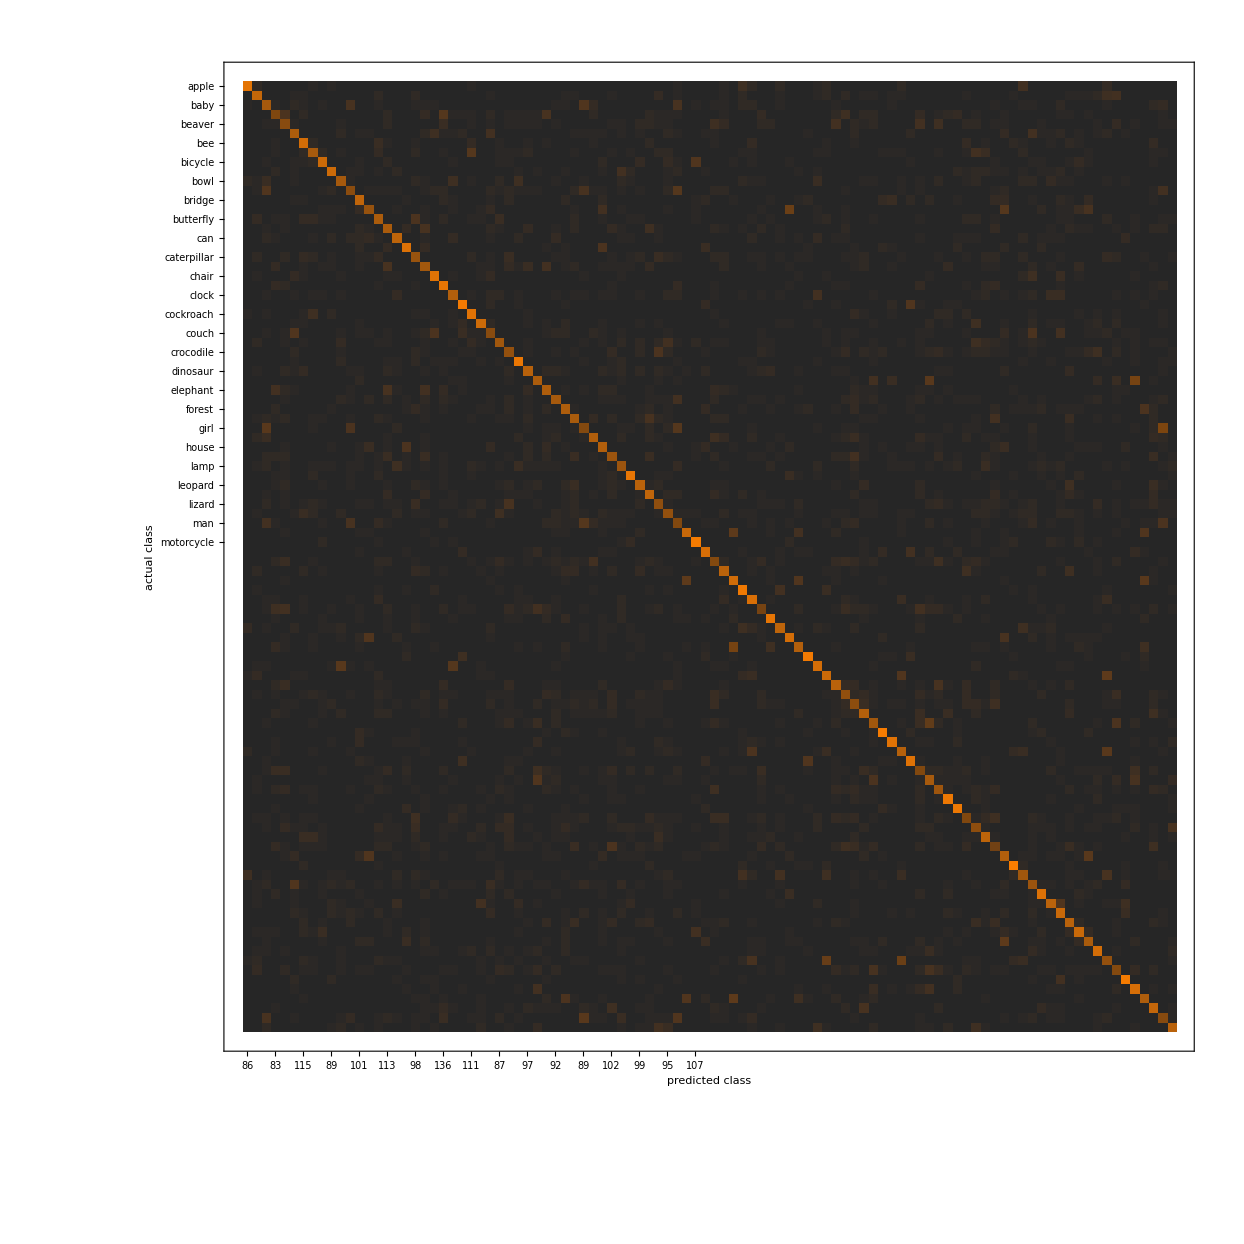
Classifier Measurements
Classifier method | Net
Number of test examples | 10000
Accuracy | (49.00.5) %
Accuracy baseline | (1.000.10) %
Geometric mean of probabilities | 0.0603 ± 0.0022
Mean cross entropy | 2.81 ± 0.036
Single evaluation time | 5.36 ms/example
Batch evaluation speed | 2.57 examples/ms
-Graphics- |

```mathematica
cm = ClassifierMeasurements[net, testData];
cm["Report"]
```

```mathematica
cm["Accuracy"->5] (* top 5 accuracy: 76% of the test examples had the correct label within the model's top5 predicted classes *)
```

0.7582

## Uniform Label Smoothing (ULS)

This is a traditional label smoothing method.  
ULS replaces the one-hot label distribution with a softened distribution for every class. 
While label smoothing emprically improves model calibration, it distorts the true labels to penalize overfitted outputs (Li et al., 2020)
In this section, I also aim to quantify this distortion.

The Formula for smoothing label for class k is as  follows: 
y'_k==(1-ϵ)·y_k+ϵ·u_k    
 (y'_k: smoothed label,  y_k: original hard label, ϵ: smoothing factor, u_k==1/K where K: total number of classes = 100)
 y_k = 1 for true class, y_k =0 for other classes.
 
 Thus,
y'_k==(1-ϵ)·0+ϵ/K==ϵ/K  (k≠C_true) 

y'_C_true==(1-ϵ)·1+ϵ/K==1-ϵ+ϵ/K (k==C_true)

#### Parameters and Label Smoothing Function

```mathematica
numClasses = Length[classes]; (* which is 100 *)
epsilon=0.1; (* smoothing strength = 0.1 *)
nonTrueValue=epsilon/numClasses ;
trueValue=1.0-epsilon+(epsilon/numClasses);

Print["Non-True Class value: ", nonTrueValue]
Print["True Class value: ",trueValue]
```

Non-True Class value: 0.001

True Class value: 0.901

```mathematica
(* Label Smoothing Function *)
(*smoothLabel[oneHot_]:=Module[{smoothedVector, trueClassIndex}, (* Module[{localvar1, ...}, body] to create local variables *)
smoothedVector=ConstantArray[nonTrueValue, numClasses]; (* ConstantArray[value, n]: a list of length n with value *)
trueClassIndex=First[Flatten[Position[oneHot, 1]]]; (* the first index of the value 1 *)
smoothedVector[[trueClassIndex]]=trueValue; (* replace 1 with the smoothed value *)
smoothedVector
];*)
```

#### Preprocess Training Data: apply Label-Smoothing to all labels

```mathematica
(*smoothedTrainingData=smoothedTrainingData/.
(Image_->ClassName_):>
(Image->
Module[{classIndex, oneHot},
classIndex=First[Position[classes,ClassName]];
oneHot=UnitVector[numClasses,classIndex];
smoothLabel[oneHot]
]); *)
```

```mathematica
classToIndex=AssociationThread[classes->Range[numClasses]];
smoothLabel[idx_Integer]:=
Module[{base=ConstantArray[nonTrueValue,numClasses]},
base[[idx]]=trueValue;
base
];
```

```mathematica
(* helper class that accepts a className and returns a smoothed vector *)
smoothLabelFromClass[className_]:=Module[{idx},
idx=Lookup[classToIndex,className,Missing["KeyAbsent"]];
If[idx===Missing["KeyAbsent"],
Message[smoothLabelFromClass::nokey, className];
Return[$Failed],
smoothLabel[idx]
]
];
```

```mathematica
pairs={#1,smoothLabelFromClass[#2]}&@@@shuffledTrainingData;
(* conversion to rule *)
smoothedTrainingData=Rule@@@pairs;
RandomSample[smoothedTrainingData, 3]
```

{-Graphics-→{0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.901,0.001,0.001},-Graphics-→{0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.901,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001},-Graphics-→{0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.901,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001}}

```mathematica
cifarNet2=NetChain[
{
(* convolution block 1*)
ConvolutionLayer[64, 3, "PaddingSize"->1], (* 3x3 convolutions *)
Ramp,
BatchNormalizationLayer[],
PoolingLayer[2, 2], (* 차원 감소 효과 *) (* 32 -> 16 *)
(* conv block 2 *)
ConvolutionLayer[128, 3, "PaddingSize"->1],
Ramp,
BatchNormalizationLayer[],
PoolingLayer[2, 2], (* 16 -> 8 *)
(* conv block 3 *)
ConvolutionLayer[256, 3, "PaddingSize"->1],
Ramp,
BatchNormalizationLayer[],
PoolingLayer[2, 2], (* 8 -> 4 *)

FlattenLayer[],

LinearLayer[512],
Ramp,
BatchNormalizationLayer[],
(*DropoutLayer[0.5], *)

LinearLayer[100], (* 100-element prob vector after SoftMaxLayer *)
SoftmaxLayer[]
},
"Input"->NetEncoder[{"Image", {32,32}}] (* removed Output port line so that it handles vector outputs *)
]
```

NetChain[…]

```mathematica
ulsNet=NetTrain[
cifarNet2,
smoothedTrainingData,
LossFunction->CrossEntropyLossLayer["Probabilities"],
ValidationSet->Scaled[0.1], (* validation set: 0.1 of trainingData *)
BatchSize->128,
MaxTrainingRounds->200,
TargetDevice->"GPU"
]
```

NetChain[<18>]

```mathematica
Export["C:\\Users\\mrkoh\\Desktop\\wolfram_project\\ulsNet.wlnet", ulsNet]
```

C:\Users\mrkoh\Desktop\wolfram_project\ulsNet.wlnet

ulsNet is now a function that maps an image into 100-element probability vector.
Therefore, the evaluation needs to be handled manually since ClassifierMeasurements[] does not work.

```mathematica
testImages=testData[[All,1]];
trueClassNames=testData[[All,2]];
```

```mathematica
predictedProbabilities=ulsNet[testImages];
(* prob. vectors -> class predictions *)
predictedIndex=Position[#,Max[#]]&/@predictedProbabilities//First/@Flatten[#,1]&;
predictedClassNames=classes[[predictedIndex]];
```

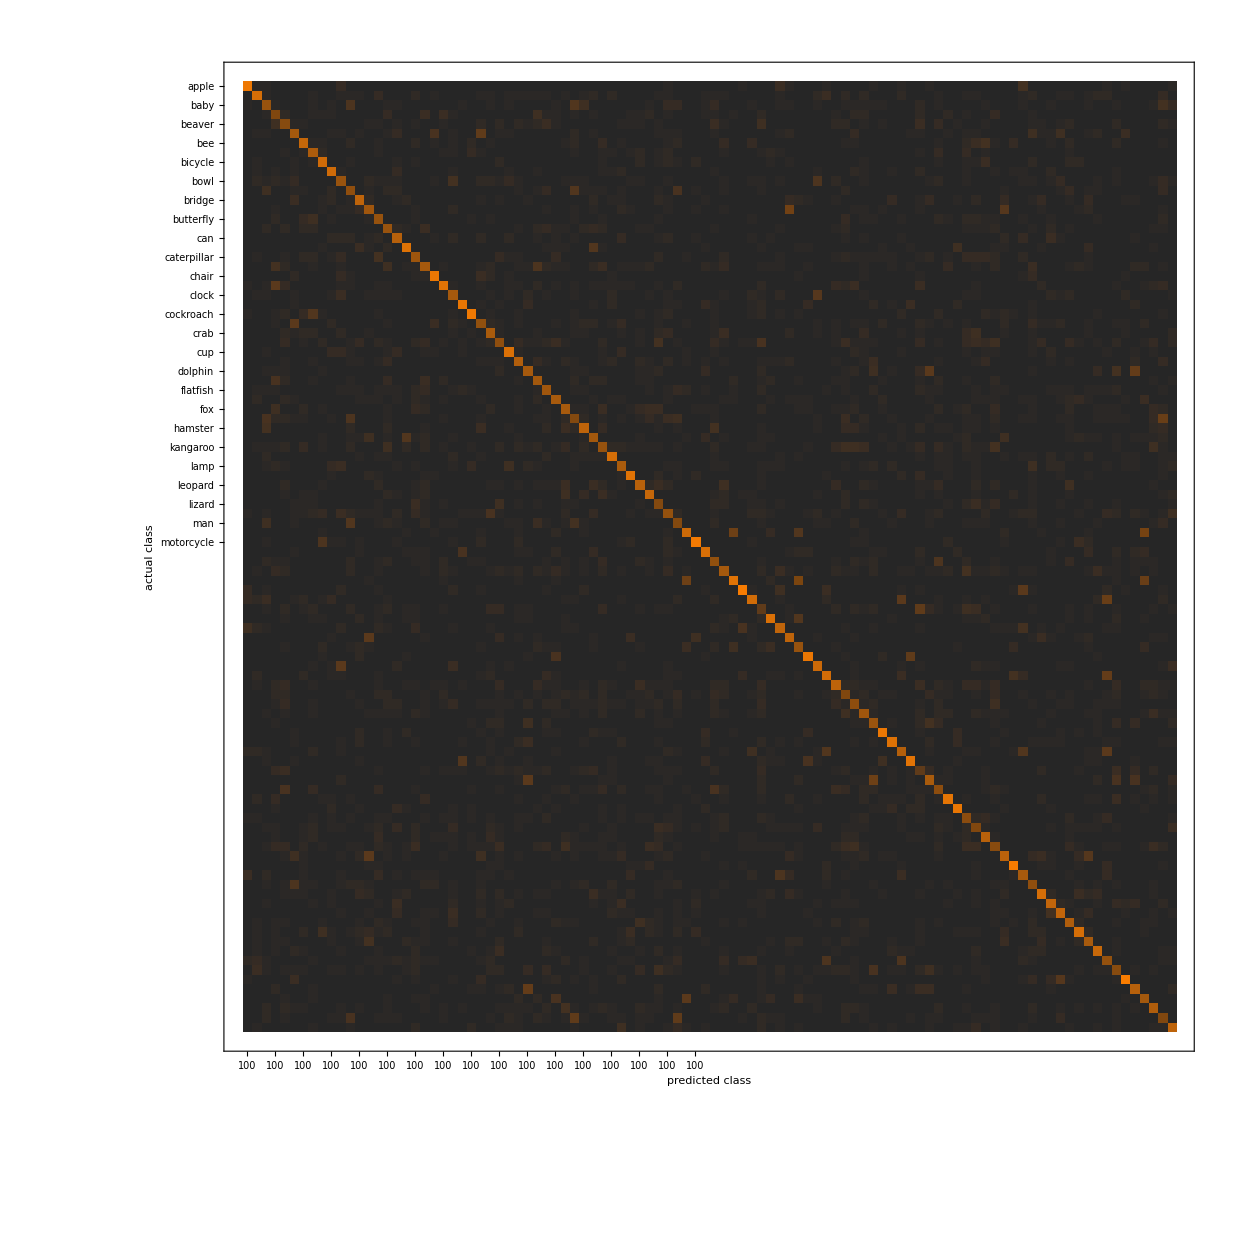
Classifier Measurements
Number of test examples | 10000
Accuracy | (47.90.5) %
Accuracy baseline | (1.330.11) %
-Graphics- |

```mathematica
cmULS=ClassifierMeasurements[trueClassNames,predictedClassNames];
cmULS["Report"]
```

```mathematica
cmULS["Accuracy"->5] (* top 5 accuracy: 50.9% of the test examples had the correct label within the model's top5 predicted classes *)
```

0.5002

The ULS did not make a significant change in the accuracy of the model.  
The lower accuracy might imply that the model is less overfitted.